# Distortion in Forward Map

We found out the the singular values of the Jacobian of a map f:ℝ^2→ℝ^2 describe the local distortion. The same thing works in ℝ^3.

We found out that we could estimate the distortion at a given point in a Forward Map (from a Poincaré section) by tracking nearby  points and using a finite-difference approximation.

We started talking about taking the gradient of the ODE
	y'=f(y) with Initial Condition y(0)=y_0
to get 
	(∇y)'=Df(y).∇y with initial condition ∇y(0)=Identity.

The plan is to compare these two techniques on our Rosseler test system and test section

## Solving the ODE for the Jacobian!

Here is our original ForwardMap modified to return the elapsed time.

```mathematica
{a,b,c}={0.2,0.2,5.7};
f[{x_,y_,z_}]:= {-y-z,x + a*y, b +z*(x-c)}
Df[{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
ForwardMap[p0_List]:=Module[{p,t,end},
Catch[
NDSolveValue[{p'[t]==f[p[t]],p[0]==p0},p,{t,0, 10^3},
Method->{"EventLocator",
"Event":>((p[t]-{0.007026204834100129,-0.035131024170500645,0.035131024170500645}). {1,-1,0}),
"EventAction":>(Throw[end={t,p[t]}];"StopIntegration"),
"Direction"->-1}]; end]
]
```

Here it is in action on a specific point. This is measuring the distortion in ℝ^3rather that just on the section

```mathematica
center={0.00702620483410129,-0.035131024170500645,0.035131024170500645};
n2=Normalize[{1.0,-1.0,0}];
ProjectOnToPlane[p_,{center_,n_}]:= p-n(p-center).n
p0=ProjectOnToPlane[{2.0,2.0,5.0},{center,n2}];
{tOut,pOut}=ForwardMap[p0];
pSol=NDSolveValue[{p'[t]==f[p[t]],p[0]==p0},p,{t,0,tOut}];
Df[{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
(* Check for Transpose Here *)
JSol = NDSolveValue[{J'[t]==Df[pSol[t]].J[t],J[0]==({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})},J,{t,0,tOut}] ;
Pic=Show[
Graphics3D[{PointSize[0.02],
{Red, Point[pOut]},{Green,Point[p0]},{Blue,Point[center]},
{Opacity[0.5],Polygon[{center,center+{5,5,0},center+{5,5,10},center+{0,0,10}}]}
}],
ParametricPlot3D[pSol[t],{t,0, tOut},PlotRange->All]
];
Manipulate[Show[
Pic, 
Graphics3D[ {PointSize[0.02],Point[pSol[t]]}]],
{{t,0.1},0, tOut}]
```

Here is what happens to a unit sphere under the linearized map.  You can not run it all the way round as it gets too thin to plot

```mathematica
Manipulate[Show[
Pic, 
Graphics3D[ Ellipsoid[pSol[t],JSol[t]]]
],
{{t,0.1},0, 0.7}]
```

To avoid the ellipsoid getting too flat I am going to plot the unit u vectors and the stretches i.e. singular values.

```mathematica
Manipulate[Show[
Pic, 
U=SingularValueDecomposition[JSol[t],3]⟦1⟧;
σs=SingularValueList[JSol[t],3];
Graphics3D[ Table[
{Hue[i/3],Arrow[{pSol[t],pSol[t]+2U⟦All,i⟧}]},{i,3}]],
PlotRange->{{-6,6},{-6,6},{0,10}},
PlotLabel->Table[{Hue[i/3],σs⟦i⟧},{i,3}]
],
{{t,0.1},0, tOut}]
```

I can put this stuff together into one command. Here  a modified ForwardMap that returns the output point, output Jacobian, and elapsed time.

```mathematica
ForwardMapPlus[p0_List]:=Module[{p,t,end,J,pSol},
Catch[
NDSolveValue[{
p'[t]==f[p[t]],p[0]==p0,
J'[t]==Df[p[t]].J[t], J[0]==({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
},p,{t,0, 10^3},
Method->{"EventLocator",
"Event":>((p[t]-{0.007026204834100129,-0.035131024170500645,0.035131024170500645}). {1,-1,0}),
"EventAction":>(Throw[end={p[t],J[t],t}];"StopIntegration"),
"Direction"->-1}]; end]
]
```

All we really have to do now is work out how to project stuff onto the Poincare section.

## Finite Difference Estimates for the ℝ^3 Jacobian!

The above is all fine and dandy but a bit fancy!  We can estimate the ℝ^3 Jacobian by solving the ODE for nearby points and doing finite differencing.  The only real problem with this trick is deciding how near is near by.

```mathematica
h=0.00001;
p0=ProjectOnToPlane[{2.0,2.0,5.0},{center,n2}]
{tOut,POut}=ForwardMap[p0]
{v1,v2,v3}={{1,0,0},{0,1,0},{0,0,1}};
{p1,p2,p3}={p0+h*v1,p0+h*v2,p0+h*v3} ;
P1 =NDSolveValue[{p'[t]==f[p[t]],p[0]==p1},p[tOut],{t,0, tOut}];
P2 =NDSolveValue[{p'[t]==f[p[t]],p[0]==p2},p[tOut],{t,0, tOut}];
P3 =NDSolveValue[{p'[t]==f[p[t]],p[0]==p3},p[tOut],{t,0, tOut}];
U={P1-POut,P2-POut,P3-POut}/h;
MatrixForm[Uᵀ]
SingularValueList[Uᵀ]
MatrixForm[J0=ForwardMapPlus[p0][[2]]]
SingularValueList[J0]
```

{2.02108,1.97892,5.}

{5.97711,{2.98977,2.94761,0.0969025}}

(1.45848 | 0.591229 | -0.313455
-0.402452 | 1.55045 | 0.163467
0.0529212 | 0.0516732 | -0.0105028)

{1.6933,1.51851,0.000472847}

(1.45839 | 0.591142 | -0.313543
-0.402347 | 1.55055 | 0.163572
0.0533286 | 0.0520806 | -0.0100951)

{1.69334,1.51848,3.83167×10^-13}

It is pretty clear that the Jacobians are pretty close and that there is a very small singular value. It is less clear exactly how tiny that singular value is.

## How much does the “transit time” vary?

The plane we chose was
	y=x-0.042157229004600776 
Here is a plot of the transit time.

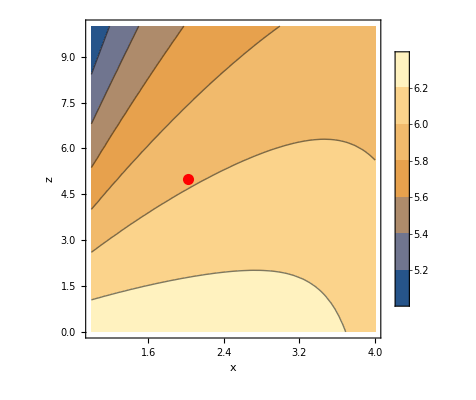

```mathematica
ContourPlot[
ForwardMap[{x,x-0.042157229004600776,z}]⟦1⟧,
{x, 1,4},{z,0, 10},
Epilog->{Red, PointSize[0.02],Point[p0⟦{1,3}⟧]},
PlotLegends->Automatic,
FrameLabel->{"x","z"},
MaxRecursion->2]
```

## Finally Putting Things onto the Poincare Section: The Jacobian of the Forward Map.

### Version 1:

We can start on the section and approximate the thing by running the same time as the center point.  In addition to the approximation to the derivative this version winds up slightly of the plane. It is not as good as the other approximations.

```mathematica
h=0.0001;
{x0,z0}={2.0,5.0};
p0={x0,x0-0.042157229004600776,z0};
{tOut,pOut}=ForwardMap[p0];
{v1,v2}={{1,1,0}/√2,{0,0,1}};
{p1,p2}={p0+h*v1,p0+h*v2} ;
{tOut,POut}=ForwardMap[p0];
P1 =NDSolveValue[{p'[t]==f[p[t]],p[0]==p1},p[tOut],{t,0, tOut}]⟦{1,3}⟧;
P2=NDSolveValue[{p'[t]==f[p[t]],p[0]==p2},p[tOut],{t,0, tOut}]⟦{1,3}⟧;
U={P1-POut⟦{1,3}⟧,P2-POut⟦{1,3}⟧}ᵀ/h;
MatrixForm[U]
SingularValueList[U]
```

(1.45421 | -0.312459
0.0718854 | -0.00971761)

{1.48916,0.00559365}

(1.45424 | -0.312429
0.0718768 | -0.00972631)

{1.48918,0.00558157}

### Version 2:

If we use the ForwardMap they all take slightly different times but do at least wind up on the plane!

```mathematica
h=0.0001;
{x0,z0}={2.0,5.0};
p0={x0,x0-0.042157229004600776,z0};
{tOut,pOut}=ForwardMap[p0];
{v1,v2}={{1,1,0}/√2,{0,0,1}};
{p1,p2}={p0+h*v1,p0+h*v2} ;
{tOut,POut}=ForwardMap[p0];
{t1,P1}=ForwardMap[p1];
{t2,P2}=ForwardMap[p2];
{P1,P2}={P1⟦{1,3}⟧,P2⟦{1,3}⟧};
U={P1-POut⟦{1,3}⟧,P2-POut⟦{1,3}⟧}ᵀ/h;
MatrixForm[U]
SingularValueList[U]
```

(1.1571 | -0.0935511
0.0659012 | -0.00532769)

{1.16276,3.8578×10^-7}

### Variation 3:

We can use the ℝ^3 Jacobian and  project onto the plane.

```mathematica
h=0.000001;
{x0,z0}={2.0,5.0};
p0={x0,x0-0.042157229004600776,z0};
{pOut,JOut,tOut}=ForwardMapPlus[p0];
Q={{1/(√2),1/(√2),0},{0,0,1}}ᵀ;
LittleJ =Qᵀ.JOut.Q;
MatrixForm[LittleJ]
SingularValueList[LittleJ]
```

(1.59938 | -0.105039
0.0718705 | -0.00972798)

{1.60446,0.00499207}